## Searching for good example rules

```mathematica
trs = ;
```

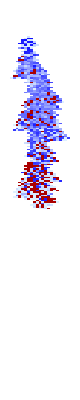
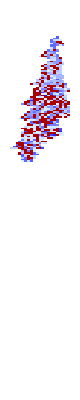
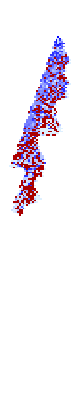
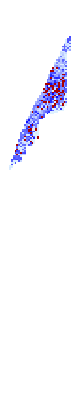
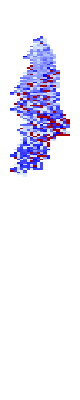
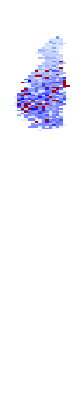
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[;;10]]]
```

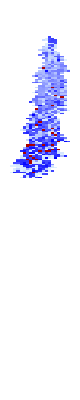
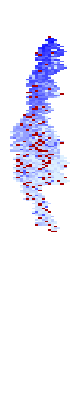
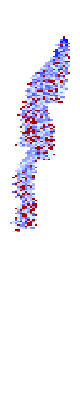
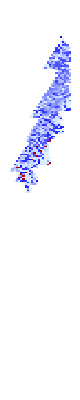
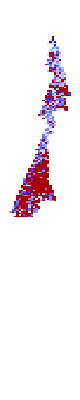
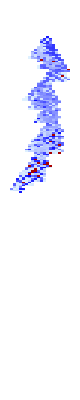
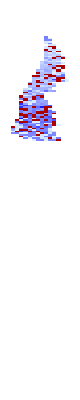
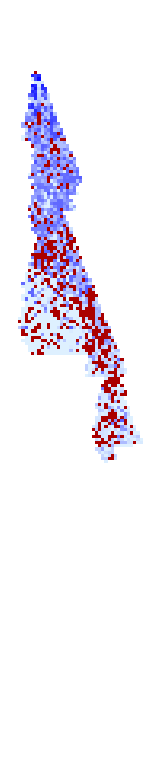

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[11;;20]]]
```

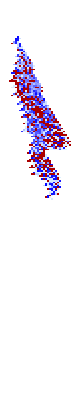
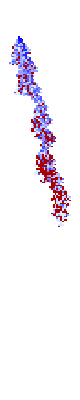
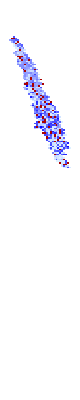
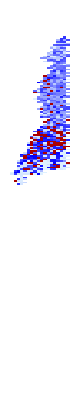
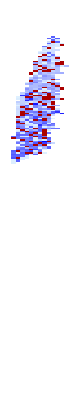
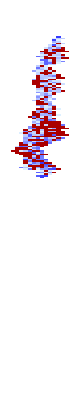
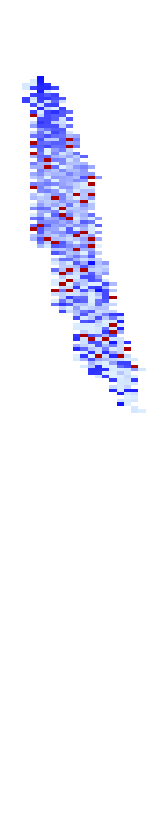
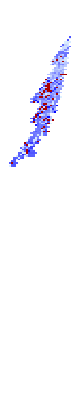
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[21;;30]]]
```

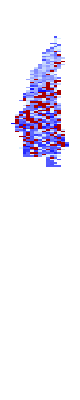
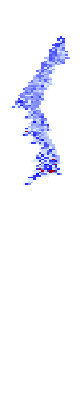
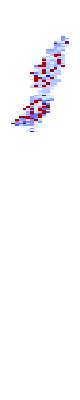
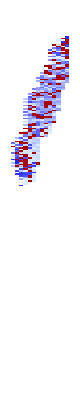
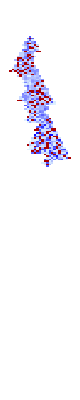
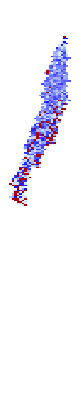
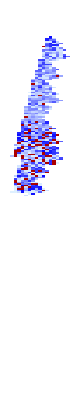
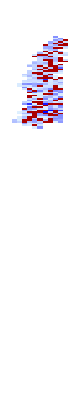
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[31;;40]]]
```

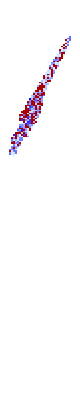
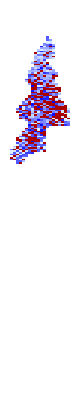
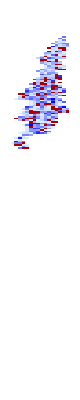
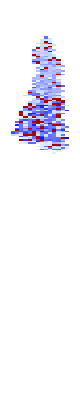
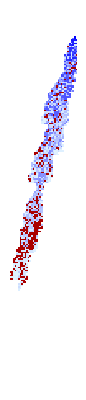
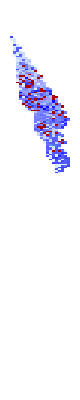
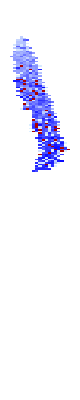
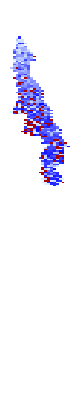
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs[[41;;52]]]
```

```mathematica
plotrule[trs[[49]]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[trs[[49]], "ReturnPerturbations"->True], 10]]
```

-Graphics-

```mathematica
trs2 = ;
```

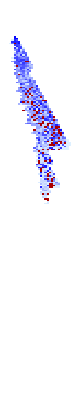
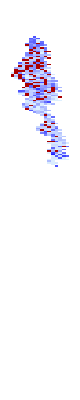
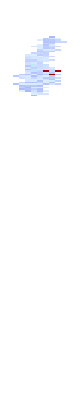
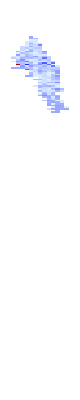
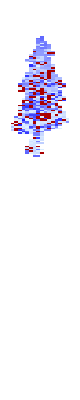
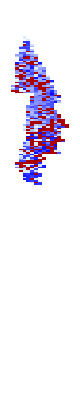
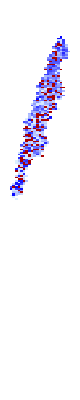
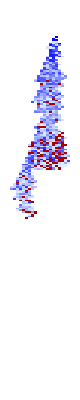

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[;;10]]]
```

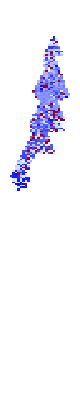
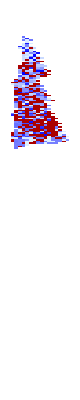
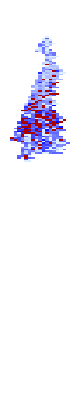
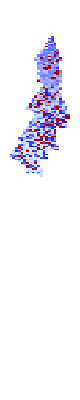
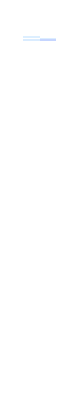
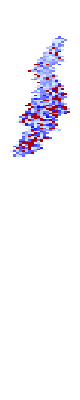
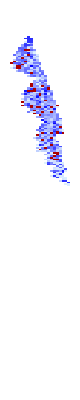
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[11;;20]]]
```

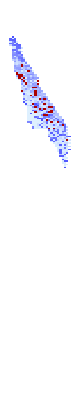
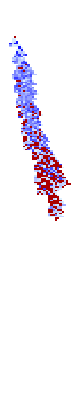
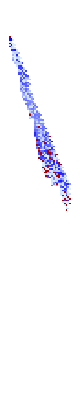
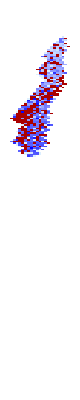
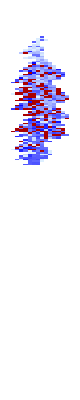
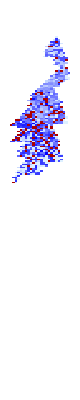
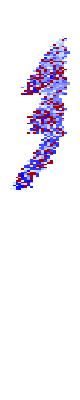
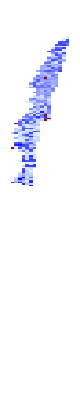
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[21;;30]]]
```

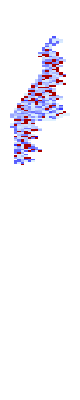
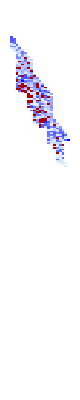
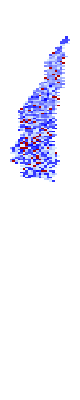
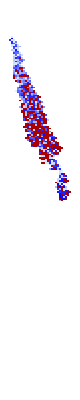
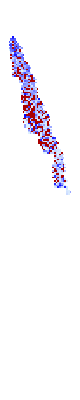
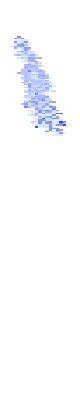
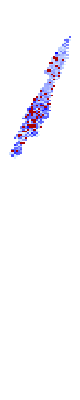
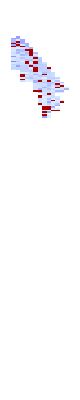
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[31;;40]]]
```

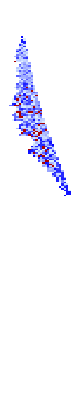
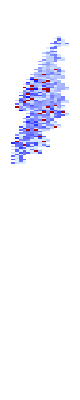
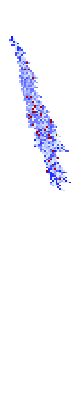
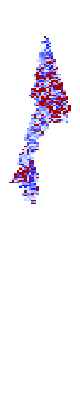
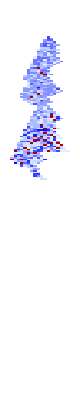
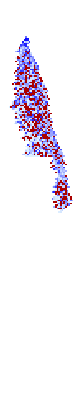
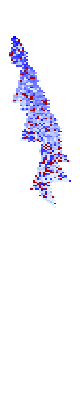
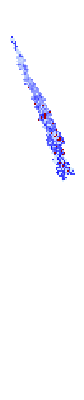
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[41;;60]]]
```

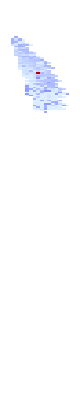
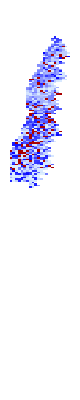
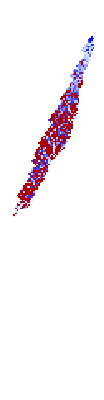
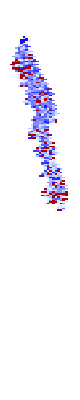
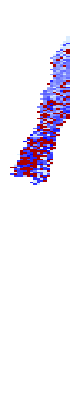
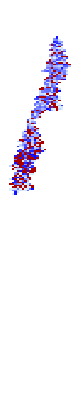
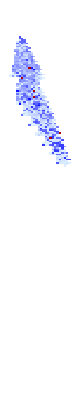
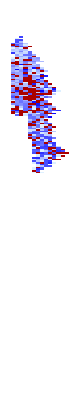
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[61;;70]]]
```

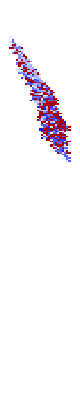
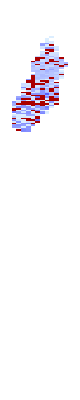
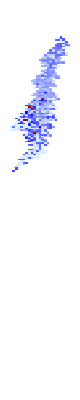
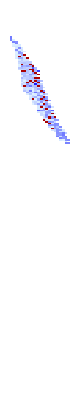
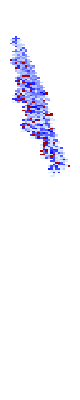
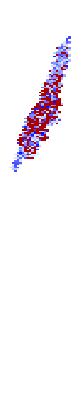
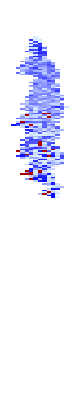
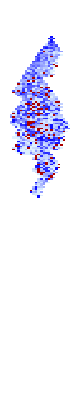
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[71;;80]]]
```

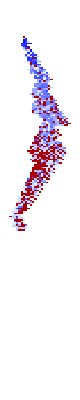
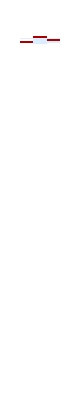
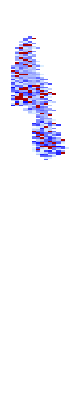
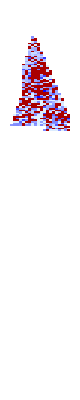
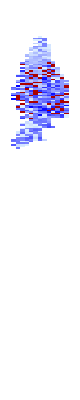
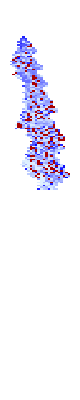
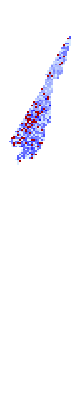
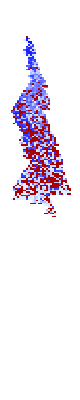

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[81;;90]]]
```

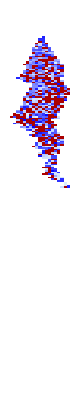
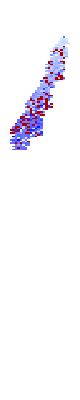
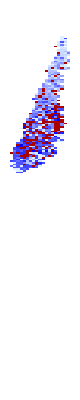
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[91;;100]]]
```

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[101;;110]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[111;;120]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[121;;130]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[131;;140]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ParallelMap[PerturbationSensitivityPlot[{getca[#], #}, absdeltalt, ("AddValue"->1)]&, trs2[[141;;148]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[trs2]
```

148

```mathematica
PlotCA[getca[trs2[[58]]]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[trs[[12]],NRandomPerts[1, getca[trs[[12]]]], "ReturnPerturbations"->True], 10]]
```

-Graphics-

## Evolving With Same Perturbations Every Time

```mathematica
perts = Transpose@{RandomInteger[{1, 100}, 50], RandomInteger[{40, 60}, 50]};
```

```mathematica
perts =Table[i->{{1}, "Enumerate"}, {i, 40}];
```

```mathematica
evo = AdaptCA[{0, 4, 1}, 1000, "AutomatonFunction"->(getca[#, 200, 100, CenterArray[1, 100]]&), "Perturbation"->perts, "ReturnCAs"->True, "ReturnPerturbations"->True, "BitFunc"->("SetValue"->0)];
```

```mathematica
GraphicsRow[PlotCA[#[[1, "cas", 2]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo
```

-Graphics-

```mathematica
PlotCA[evo[[-1, "rule"]]]
```

-Graphics-

```mathematica
With[{ca =getca[evo[[-1, "rule"]], 200, 100, CenterArray[1, 100]]},RandomChoice[Flatten[getbodyidxs[ca]]]]
```

45

```mathematica
With[{ca =getca[evo[[-1, "rule"]], 200, 100, CenterArray[1, 100]]}, Table[PlotCA[PerturbCA[evo[[-1, "rule"]],perts]], 10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PerturbCA[{getca[evo[[-1, "rule"]], 200, 100, CenterArray[1, 100]], evo[[-1, "rule"]]}, {1, 1}]
```

```mathematica
PerturbationSensitivityPlot[{getca[evo[[-1, "rule"]], 200, 100, CenterArray[1, 100]], evo[[-1, "rule"]]}, absdeltalt, ("SetValue"->0)]
```

-Graphics-

```mathematica
Intersection[{{1, 1}}, {{1, 1}, {1, 2}}]
```

{{1,1}}

## Evolving Genetic Robustness

```mathematica
geneticpertfunc[{ca_, ru_}]:= getca[RandomRuleMutation[ru], Length[ca]]
```

```mathematica
SeedRandom[4600];
evo = AdaptCA[{0, 5, 1}, 2000,"PerturbationFunction"->geneticpertfunc, "NPerturbations"->5];
evo[[-1, "fitness"]]
GraphicsRow[PlotCA[#[[1,"rule"]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo
```

37

-Graphics-

```mathematica
plotrule[evo[[-1, "rule"]]]
```

-Graphics-

```mathematica
evo[[-1, "rule"]]
```

{63603350490056248387374234882853345539893717923014906631901432550947254713231151216225,5,1}

```mathematica
plotmaskedrule[evo[[-1, "rule"]], ImageSize->1000]
```

-Graphics-

```mathematica
Table[PlotCA[RandomRuleMutation[evo[[-1, "rule"]]]], 5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Takeaway: Genetic robustness is much harder than robustness to perturbations. Why? Unclear

```mathematica
Histogram[Table[TestLifetime[{{"[◼]", "RandomRuleMutation"}}[ evo[[-1, "rule"]]], 200], 1000]/.-Infinity->0]
```

-Graphics-

### Regular for comparison

```mathematica
SeedRandom[333775];
evo3 = AdaptCA[{0, 4, 1}, 1000, "ReturnCAs"->True, "ReturnPerturbations"->True];
```

```mathematica
GraphicsRow[PlotCA[#[[1,"rule"]](*, "Trim"->{None, None}*)]&/@ GatherBy[#, #fitness&]]&@evo3
```

-Graphics-

```mathematica
plotmaskedrule[GatherBy[evo3, #fitness&][[5, 1, "rule"]]]
```

-Graphics-

```mathematica
PlotCA[GatherBy[evo3, #fitness&][[5, 1, "rule"]]]
```

-Graphics-

```mathematica
Histogram[Table[TestLifetime[{{"[◼]", "RandomRuleMutation"}}[GatherBy[evo3, #fitness&][[5, 1, "rule"]]], 200], 1000]/.-Infinity->0]
```

-Graphics-

## Kicking the tv

## Multiway Graph

## Drugs

## Clinical Trials on Other Rules

## New AdaptCA function for larger search

With support for perturbation specifications

```mathematica
SeedRandom[333768];
evo = AdaptCA[{0, 4, 1}, 500,   "ReturnCAs"->True, "Perturbation"->True, "NPerturbations"->2, "ReturnPerturbations"->True];
```

And support for drawing arrows

```mathematica
GraphicsGrid[Partition[GraphicsRow[#]& /@(PlotCA[#(*, "Trim"->{1, 10}*)]&/@#[[1, "cas"]]&/@ GatherBy[evo, #fitness&]), 5], ImageSize->1000]
```

-Graphics-

### TODO: Magnification

## Running more evolutions

```mathematica
evos = ParallelTable[SeedRandom[4468+ i];
 AdaptCA[{0, 4, 1}, 1000, "Perturbation"->("NRandom"->3),"NPerturbations"->5], {i, 3}];
```

```mathematica
GraphicsRow[PlotCA[#[[1, "rule"]]]&/@ GatherBy[#, #fitness&]]&/@ evos
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[Table[PlotCA@PerturbCA[evos[[2, -1, "rule"]],"NRandom"->1], 10]]
```

-Graphics-